```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
$K=9;
Do[data[k] = {}, {k, 2, 1+$K($K+1)}];
Do[Module[{}, (
d = Import["../../../backup/mar-14/Stats-101/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 2, 3}];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 4, 1+$K($K+1), 1}];
)], {$N, 3, 9}]
```

```mathematica
fig[1] = ListPlot[data[2],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotLabel->MaTeX@"\\expval{\\Tr X^2}_t",
FrameLabel->{MaTeX@"N", None},
FrameTicks->{{With[{ticks=1.5+0.3Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->7.4cm
];
```

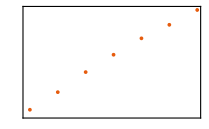

```mathematica
Magnify[fig[1], 1]
```

```mathematica
fig[2] = ListPlot[data[3],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotLabel->MaTeX@"\\sigma(\\Tr X^2)_t",
FrameLabel->{MaTeX@"N", None},
FrameTicks->{{With[{ticks=0.0+0.1Range[0,20]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,20]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->All,
ImageSize->7.4cm
];
```

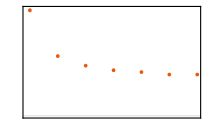

```mathematica
Magnify[fig[2], 1]
```

```mathematica
plt[1]=Grid[{{fig[1], "",  fig[2]}}]
```

-Graphics- |  | -Graphics-

```mathematica
Export[plotsDir<>"/4-monopole.pdf", plt[1]]
```

../../../plots/plots-thesis/4-monopole.pdf

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
latexExp[i_, j_] := Module[{}, (
If[i == j, 
"\\frac{8}{"<>ToString@$K<>"}\\Tr (X^{"<>ToString@i<>"})^2"<>" - \\frac{1}{"<>ToString@$K<>"}\\sum_{i=2}^{9} \\Tr(X^{i})^2 ",
"\\Tr X^{"<>ToString@i<>"} X^{"<>ToString@j<>"}"
]
)];
```

```mathematica
fig[3] = ListPlot[Table[Table[{data[k][[A, 1]]+0.05(k-9), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 4, 14, 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotLabel->MaTeX@"\\expval{\\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2}_t",
FrameLabel->{MaTeX@"N", None},
FrameTicks->{{With[{ticks=-0.2+0.05Range[0,10]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{Automatic, {-0.14, 0.14}},
ImageSize->7.4cm
];
```

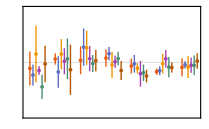

```mathematica
Magnify[fig[3], 1]
```

```mathematica
fig[4] = ListPlot[Table[Table[{data[k][[A, 1]]+0.05(k-10), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 5, 15, 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
PlotLabel->MaTeX@"\\sigma \\left( \\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2 \\right)_t",
FrameLabel->{MaTeX@"N", None},
FrameTicks->{{With[{ticks=0+0.1Range[0,10]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{Automatic, {0, 0.6}},
ImageSize->7.4cm
];
```

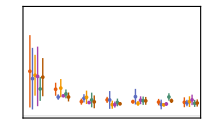

```mathematica
Magnify[fig[4], 1]
```

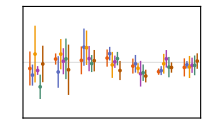
-Graphics- |  | -Graphics-
 |  | 
 |  | 
 |  | 
 |  |

```mathematica
plt[2]=Legended[Grid[{{fig[3], "",  fig[4]}, {"", "", ""}, {"", "", ""}, {"", "", ""}, {"", "", ""}}], Placed[PointLegend[colors[[1;;6]], (MaTeX/@Flatten@Table[latexExp[i, j], {i, 1, $K-1}, {j, i, $K}]), LegendLayout->"Row"], {Bottom, Center}]]
```

```mathematica
Export[plotsDir<>"/4-quadrupole.pdf", plt[2]]
```

../../../plots/plots-thesis/4-quadrupole.pdf

```mathematica
x[1] = Import["../../../runs/Trials/N9K9/12279703.dat"];
```

```mathematica
x[2] = Import["../../../runs/Trials/N9K9/15650383.dat"];
```

```mathematica
x[3] = Import["../../../runs/Trials/N9K9/21385198.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rad[1] = radius/@x[1];
```

```mathematica
rad[2] = radius/@x[2];
rad[3] = radius/@x[3];
```

```mathematica
l = RandomSample[rad[1][[All, 2]], 20000];
```

```mathematica
l//Dimensions
```

{5000}

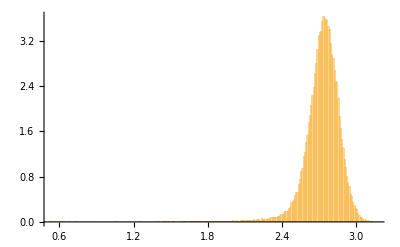

```mathematica
Histogram[Table[rad[a][[All, 2]], {a, 1}], 300, PDF]
```

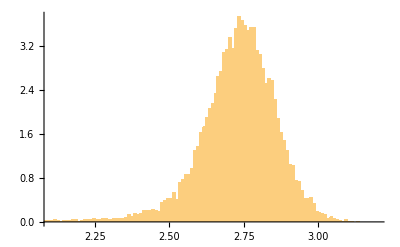

```mathematica
Histogram[{l, 300, PDF,
PlotRange->{{2.1, 3.2}, Automatic}
]
```